```mathematica
R = {{1/(√2),-1/(√2),0},{1/(√6),1/(√6),-2/(√6)},{1/(√3),1/(√3),1/(√3)}};
MatrixForm[Simplify[Inverse[R]]]
```

(1/(√2) | 1/(√6) | 1/(√3)
-1/(√2) | 1/(√6) | 1/(√3)
0 | -√(2/3) | 1/(√3))

```mathematica
m[ϕ_,θ_]:={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],Sin[θ]};
q = -1; (*vorticity*)

α1[ψ_,αx_,αy_] :=q(ψ+ λ( +αy/(√6)+αx/(√2)));
α2[ψ_,αx_,αy_] := q( ψ+λ(-αx/(√2)+αy/(√6)));
α3[ψ_,αx_,αy_] :=q(ψ+ λ(- √(2/3)αy ));

β1[β0_,βx_,βy_] :=  λ (β0/(√3) + βy/(√6)+βx/(√2));
β2[β0_,βx_,βy_] :=  λ (β0/(√3) + βy/(√6)-βx/(√2));
β3 [β0_,βx_,βy_] :=λ (β0/(√3) - √(2/3)βy);

m1 = m[ α1[ψk,ax,ay]+q (2π)/3,q β1[0,0,0]];
m2 = m[ α2[ψk,ax,ay]+q (4π)/3,q β2[0,0,0]];
m3 = m[ α3[ψk,ax,ay],q β3[0,0,0]];

(*m1 = m[q α1[ψk,ax,ay]+q (2π)/3,q β1[b0,bx,by]];
m2 = m[q α2[ψk,ax,ay]+q (4π)/3,q β2[b0,bx,by]];
m3 = m[q α3[ψk,ax,ay],q β3[b0,bx,by]];*)

n1 = m[(2π)/3,0]; (* rotate by π/2 to change compounds*)
n2 = m[(4π)/3,0];
n3 = m[(6π)/3,0];
```

```mathematica
(*magnetizations in plane*)
mx = {1,0,0}.(m1+m2+m3);
Print["magnetizations m_x and m_y for the total plaquette"]
Simplify[Series[mx,{λ,0,1}]]
my = {0,1,0}.(m1+m2+m3);
Simplify[Series[my,{λ,0,1}]]
```

magnetizations m_x and m_y for the total plaquette

√(3/2) (-ax Cos[ψk]+ay Sin[ψk]) λ+O[λ]^2

√(3/2) (ay Cos[ψk]+ax Sin[ψk]) λ+O[λ]^2

```mathematica
mxi = √(3/2)(-ax Cos[ψk]+ay Sin[ψk]);
myi =√(3/2)(ay Cos[ψk]+ax Sin[ψk]);
```

```mathematica
(*Exchange energy*)
Hex = m1.m2 + m2.m3 + m1.m3;
Simplify[Series[Hex,{λ,0,2}]]
```

-3/2+3/4 (ax^2+ay^2) λ^2+O[λ]^3

```mathematica
(* distances under strain*)
p3 = {0,0};
p1 = {(ω uxdx) + 1, ω uydx};
p2 = {1/2+1/2(ω uxdx) + (√3)/2(ω uxdy),(√3)/2+(√3)/2(ω uydy) + 1/2(ω uydx)};
p32 = Sqrt[(p3-p2).(p3-p2)];
p31 =  Sqrt[(p3-p1).(p3-p1)];
p12 =  Sqrt[(p1-p2).(p1-p2)];

Series[p32,{ω,0,1}]
Series[p12,{ω,0,1}]
Series[p31,{ω,0,1}]
```

1+1/4 (uxdx+√3 uxdy+√3 uydx+3 uydy) ω+O[ω]^2

1+1/4 (uxdx-√3 uxdy-√3 uydx+3 uydy) ω+O[ω]^2

1+uxdx ω+O[ω]^2

```mathematica
l21 = 1+ϵxx;
l31 = 1+1/4 (ϵxx+2 √3 ϵxy+3 ϵyy) ;
l23= 1+1/4 (ϵxx-2 √3 ϵxy+3 ϵyy) ;
hpressure = ((l23 m2.m3)+(l31 m3.m1)+(l21 m2.m1)-( m1.m2 + m2.m3 + m1.m3));
Simplify[Series[hpressure,{λ,0,1}]]
```

-(3 (ϵxx+ϵyy))/4-3/4 (√(3/2) (2 ay ϵxy+ax (-ϵxx+ϵyy))) λ+O[λ]^2

```mathematica
(*Zeeman energy*)
B = h{Cos[ψh],Sin[ψh],0};
hZeeman = -(m1+m2+m3).B;
FullSimplify[Series[hZeeman,{λ,0,1}]]
```

√(3/2) h (ax Cos[ψh+ψk]-ay Sin[ψh+ψk]) λ+O[λ]^2

```mathematica
(*Local anisotropy*)
```

```mathematica
Hloc =-δ((n1.m1)^2 + (n2.m2)^2 + (n3.m3)^2 );
Simplify[Series[Hloc,{λ,0,2}]]
```

-(3 δ)/2+√(3/2) δ (ax Cos[2 ψk]-ay Sin[2 ψk]) λ-1/2 (δ ((ax^2-ay^2) Cos[2 ψk]+2 ax ay Sin[2 ψk])) λ^2+O[λ]^3

```mathematica
(*GATHERING ENERGIES*)(*MX = cosϕ , MY = sinϕ*) (*if we take proportions h = √(3/2)= aniso , strain = 3/2 √(3/2), exchange = 3*)
exchange = (3J)/4(ax^2+ay^2);
strain = √(3/2) ϵ(- ay Sin[2ψϵ]+ax Cos[2ψϵ]);
zee = √(3/2) h (ax Cos[ψh+ψk]-ay Sin[ψh+ψk]);
aniso =+√(3/2) δ (ax Cos[2 ψk]-ay Sin[2 ψk]) -1/2 (δ ((ax^2-ay^2) Cos[2 ψk]+2 ax ay Sin[2 ψk]))  ;
Etot = exchange + strain+zee+aniso;
```

```mathematica
Simplify[Series[Etot,{ax,0,2},{ay,0,2}]]
```

(-√(3/2) (δ Sin[2 ψk]+h Sin[ψh+ψk]+ϵ Sin[2 ψϵ]) ay+(3 J ay^2)/4+O[ay]^3)+√(3/2) (δ Cos[2 ψk]+h Cos[ψh+ψk]+ϵ Cos[2 ψϵ]) ax+(3 J ax^2)/4+O[ax]^3

```mathematica
e1 = D[Etot,ax]; 
e2= D[Etot,ay];
sol = Simplify[Solve[e1==0&&e2==0,{ax,ay}]];
Print["Solutions for distortions"]
Print["ax:"]
ax= Simplify[sol[[1,1,2]]]  (*Subscript[Mn, 3] Ge*)
Print["ay:"]
ay=Simplify[sol[[1,2,2]]]
```

Solutions for distortions

ax:

-(√6 (3 J δ Cos[2 ψk]+2 δ^2 Cos[4 ψk]+3 h J Cos[ψh+ψk]+2 h δ Cos[ψh+3 ψk]+3 J ϵ Cos[2 ψϵ]+2 δ ϵ Cos[2 (ψk+ψϵ)]))/(9 J^2-4 δ^2)

ay:

(√6 (3 J δ Sin[2 ψk]-2 δ^2 Sin[4 ψk]+3 h J Sin[ψh+ψk]-2 h δ Sin[ψh+3 ψk]+3 J ϵ Sin[2 ψϵ]-2 δ ϵ Sin[2 (ψk+ψϵ)]))/(9 J^2-4 δ^2)

```mathematica
Energy= Etot;
Print["The total energy after minima of hard fields used."]
FullSimplify[Energy]
Print["Induced magnetization mx my"]
FullSimplify[Series[mxi,{h,0,1}]]
FullSimplify[Series[myi,{h,0,1}]]
```

The total energy after minima of hard fields used.

-1/(18 J^2-8 δ^2)3 (3 J (h^2+δ^2+ϵ^2)+6 h J δ Cos[ψh-ψk]+2 (δ^3 Cos[6 ψk]+h^2 δ Cos[2 (ψh+2 ψk)]+2 h δ^2 Cos[ψh+5 ψk]+3 h J ϵ Cos[ψh+ψk-2 ψϵ]+3 J δ ϵ Cos[2 (ψk-ψϵ)]+2 δ^2 ϵ Cos[2 (2 ψk+ψϵ)]+δ ϵ^2 Cos[2 (ψk+2 ψϵ)]+2 h δ ϵ Cos[ψh+3 ψk+2 ψϵ]))

Induced magnetization mx my

(9 J δ Cos[ψk]+9 J ϵ Cos[ψk-2 ψϵ]+6 δ (δ Cos[5 ψk]+ϵ Cos[3 ψk+2 ψϵ]))/(9 J^2-4 δ^2)+((9 J Cos[ψh]+6 δ Cos[ψh+4 ψk]) h)/(9 J^2-4 δ^2)+O[h]^2

(9 J δ Sin[ψk]-9 J ϵ Sin[ψk-2 ψϵ]-6 δ (δ Sin[5 ψk]+ϵ Sin[3 ψk+2 ψϵ]))/(9 J^2-4 δ^2)+((9 J Sin[ψh]-6 δ Sin[ψh+4 ψk]) h)/(9 J^2-4 δ^2)+O[h]^2

```mathematica
(*Emergent Landau functional*)
functional1 =-(+2 h δ Cos[ψh-ψk]+2 h ϵ Cos[ψh+ψk-2 ψϵ]+2 δ ϵ Cos[2 (ψk-ψϵ)])/(2 J);
Simplify[functional1]
```

-(h δ Cos[ψh-ψk]+h ϵ Cos[ψh+ψk-2 ψϵ]+δ ϵ Cos[2 (ψk-ψϵ)])/J

```mathematica
(*functional with anisotropy δ to second order*)
functional2 = -1/(18 J^2)3 (3 J (h^2+δ^2+ϵ^2)+6 h J δ Cos[ψh-ψk]+2 (δ^3 Cos[6 ψk]+h^2 δ Cos[2 (ψh+2 ψk)]+2 h δ^2 Cos[ψh+5 ψk]+3 h J ϵ Cos[ψh+ψk-2 ψϵ]+3 J δ ϵ Cos[2 (ψk-ψϵ)]+2 δ^2 ϵ Cos[2 (2 ψk+ψϵ)]+δ ϵ^2 Cos[2 (ψk+2 ψϵ)]+2 h δ ϵ Cos[ψh+3 ψk+2 ψϵ])); 
ϵ = 0;
Simplify[functional2]
Clear[ϵ]
```

-(3 J (h^2+δ^2)+6 h J δ Cos[ψh-ψk]+2 δ^3 Cos[6 ψk]+2 h δ (h Cos[2 (ψh+2 ψk)]+2 δ Cos[ψh+5 ψk]))/(6 J^2)

```mathematica
(*FULL FUNCTIONAL*)
f4=-(h δ Cos[ψh-ψk]+h ϵ Cos[ψh+ψk-2 ψϵ]+δ ϵ Cos[2 (ψk-ψϵ)])/J;
```

500

Angles for the strain field and the magnetic field

0

0.000174533

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

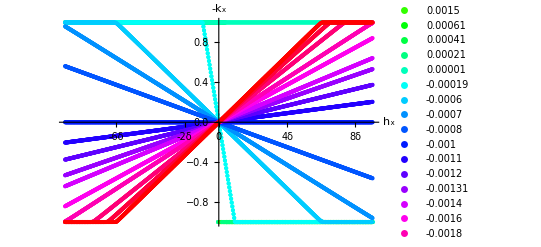

```mathematica
J = 1;
a = 1/100;
δ = .1 a ;
hext = 9 δ;
hi=hext;
n = 500(*mag field steps*)
Print["Angles for the strain field and the magnetic field"]
ψϵ = (0π)/180(*fix the misallignment angles*)
ψh = (0.01π)/180

(*straintens = a{0.150,0.061,0.041,0.021,.011,0.001,-0.019,-0.060,-0.070,-0.080,-0.100,-0.110,-0.120,-0.131,-0.140,-0.160,-0.180,-0.220,-0.261,-0.301};*)
(*Satoru's data*)
straintens = a{0.150,0.061,0.041,0.021,.001,-0.019,-0.060,-0.070,-0.080,-0.100,-0.110,-0.12,-0.131,-0.14,-0.160,-0.180,-0.22,-0.261,-0.301};

lmax = Length[straintens];

hall= Table[0,{i,n}];
plotmat = Table[i,{i,n},{j,2}];
plots1 = Table[0,{i,Length[straintens]}];
hue=Table[{0.3+0.7((l-1)/(lmax-1))},{l,1,lmax}]; (* colors for individual plots*)


For[j = 1,j≤ Length[straintens],j++,
ϵ = straintens[[j]];
h =  hi;
start = 0;

For[i = 1, i≤ n,i++,
v = FindMinimum[f4,{ψk,start},AccuracyGoal->12,PrecisionGoal->40];(*only care about mx*)
hall[[i]] =-Cos[v[[2,1,2]]];
start = v[[2,1,2]];
plotmat[[i,2]]=hall[[i]];
plotmat[[i,1]]=h Cos[ψh];
h = hi-(((2 hi)/n)i);
];
 p1 = ListLinePlot[plotmat,PlotStyle->{Hue[hue[[j]]]},BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel-> {Style["h_x",Bold,16],Style["-k_x",Bold,16]},Ticks->{{{-2δ,"-2δ"},{-4δ,"-4δ"},{-6δ,"-6δ"},{-8δ,"-8δ"},0,{2δ,"2δ"},{4δ,"4δ"},{6δ,"6δ"},{8δ,"8δ"}},Automatic},PlotStyle->Thickness[.04], PlotRange->All(*,PlotLegends->{ϵ}*)];
plots1[[j]] = p1;
Clear[ϵ];
Clear[h];
Clear[start];
]

(*Show[plots1]*)

hi=- hext;

hall= Table[0,{i,n}];
plotmat = Table[i,{i,n},{j,2}];
plots2 = Table[0,{i,Length[straintens]}];

For[j = 1,j≤ Length[straintens],j++,
ϵ = straintens[[j]];
h =  hi;
start = 0;
For[i = 1, i≤ n,i++,
v = FindMinimum[f4,{ψk,start},AccuracyGoal->10,PrecisionGoal->40];(*only care about mx*)
hall[[i]] =-Cos[v[[2,1,2]]];
start = v[[2,1,2]];
plotmat[[i,2]]=hall[[i]];
plotmat[[i,1]]=h Cos[ψh];
h = hi-(((2 hi)/n)i);
];
 p1 = ListLinePlot[plotmat,PlotStyle->{Hue[hue[[j]]]},BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel-> {Style["h_x",Bold,16],Style["-k_x",Bold,16]},Ticks->{{{-2δ,"-2δ"},{-4δ,"-4δ"},{-6δ,"-6δ"},{-8δ,"-8δ"},0,{2δ,"2δ"},{4δ,"4δ"},{6δ,"6δ"},{8δ,"8δ"}},Automatic}, PlotStyle->Thickness[.04], PlotRange->All,PlotLegends->{Style[ϵ,Bold]}];
plots2[[j]] = p1;
Clear[ϵ];
Clear[h];
Clear[start];
]

(*Show[plots2]*)
(*plotting Hysterisis loops*)
plotsh = Join[plots1,plots2];
Show[plotsh]
```

```mathematica
Clear[ax];
Clear[ay];

Clear[ϵ];
Clear[h];

Clear[mxi];
Clear[myi];

Clear[ψϵ];
Clear[ψh];

Clear[J];
Clear[δ];
```

```mathematica
5.8*10^-5*2*10^3(*meV for Zeeman energy*)
```

0.116

```mathematica
m = FindMinimum[(Cos[ψ])^2,{ψ,0.01},AccuracyGoal->11,PrecisionGoal->40]
m[[2,1,2]]
```

{3.7494×10^-33,{ψ→1.5708}}

1.5708

```mathematica
(*SIMPLIFIED VERSIONS OF THE FUNCTIONAL*)
ψh = 0;
ψϵ = 0;
fhϵ = Simplify[f4]
Clear[ψh]
Clear[ψϵ]
```

-(h (δ+ϵ) Cos[ψk]+δ ϵ Cos[2 ψk])/J

```mathematica
Solve[D[fhϵ,ψk] == 0,ψk]
```

{{ψk→ConditionalExpression[2 π C[1],C[1]∈Integers]},{ψk→ConditionalExpression[π+2 π C[1],C[1]∈Integers]},{ψk→ConditionalExpression[ArcTan[(-h δ-h ϵ)/(4 δ ϵ),-(√(-h^2 δ^2-2 h^2 δ ϵ-h^2 ϵ^2+16 δ^2 ϵ^2))/(4 δ ϵ)]+2 π C[1],C[1]∈Integers]},{ψk→ConditionalExpression[ArcTan[(-h δ-h ϵ)/(4 δ ϵ),(√(-h^2 δ^2-2 h^2 δ ϵ-h^2 ϵ^2+16 δ^2 ϵ^2))/(4 δ ϵ)]+2 π C[1],C[1]∈Integers]}}

```mathematica
Show[bp,Ticks->{{0,{Pi/2,""},Pi,{3 Pi/2,""},2 Pi,{5 Pi/2,""},3 Pi},Automatic}]
```